Грицак А.В. ПО-4
Лабораторная работа №1

Раздел 1.1
1. Используя функцию Range создайте список {1,2,3,4}

```mathematica
Range[4](*функция создает список от 1 до 4*)
```

{1,2,3,4}

2. Создайте список из натуральных чисел от 1 до 100

```mathematica
Range[100](* функция создает список от 1 до 100*)
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

3. Используя функции Range и Reverse, создайте список {4,3,2,1}

```mathematica
Reverse[Range[4]](*range создает список от 1 до 4, а reverse ставит члены списка в обратном порядке*)
```

{4,3,2,1}

4. Создайте список из натуральных чисел от 1 до 50 в обратном порядке

```mathematica
Reverse[Range[50]](*range создает список от 1 до 50, а reverse ставит члены списка в обратном порядке*)
```

{50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

5. Используя функции Range, Reverse и Join, создайте список {1,2,3,4,4,3,2,1}

```mathematica
Join[Range[4],Reverse[Range[4]]](*range создает список от 1 до 4, reverse ставит члены списка в обратном порядке, join объединяет два списка*)*)
```

{1,2,3,4,4,3,2,1}

6. Нарисовать график списка чисел, которые возрастают от 1 до 100, а затем убывают от 100 
до 1

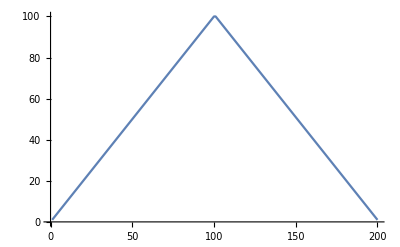

```mathematica
ListLinePlot[Join[Range[100],Reverse[Range[100]]]](*listlineplot строит прямую через точки*)
```

7. Используя функции Range и RandomInteger создайте список случайно генерированной
длины, не превышающей число 10

```mathematica
Range[RandomInteger[10]](*Randominteger генерирует случайные числа не больше чем 10*)
```

{1,2,3,4,5,6}

8. Найти простейшую форму для команды Reverse[Reverse[Range[10]]]

```mathematica
Range[10] (* первый reverse переворачивает список так что элементы идут в обратном порядке*)
(* второй reverse переворачивает обратный список и элементы опять расположены в прямом порядке*)
```

{1,2,3,4,5,6,7,8,9,10}

9. Найти простейшую форму для команды Join[{1,2},Join[{3,4},{5}]]

```mathematica
Range[5](*результат выполнения команды из условия это список от 1 до 5*)
```

{1,2,3,4,5}

10. Найти простейшую форму для команды Join[Range[10],Join[Range[10],Range[5]]]

```mathematica
Join[Range[10],Range[10],Range[5]]
```

{1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5}

11. Найти простейшую форму для команды Reverse[Join[Range[20],Reverse[Range[20]]]]

```mathematica
Join[Range[20],Reverse[Range[20]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

Раздел 1.2

1. Присоедините две копии строки «Здравствуйте».

```mathematica
StringJoin["Здравствуйте","Здравствуйте"](*stringjoin объединяет строки в одну*)
```

ЗдравствуйтеЗдравствуйте

2. Создайте единую строку всего английского алфавита заглавными буквами.

```mathematica
ToUpperCase[Alphabet[]](*alphabet выводит алфавит(латиница по умолчанию), touppercase делает буквы заглавными*)
```

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z}

3. Сгенерируйте строку английского алфавита в обратном порядке.

```mathematica
Reverse[Alphabet[]]
```

{z,y,x,w,v,u,t,s,r,q,p,o,n,m,l,k,j,i,h,g,f,e,d,c,b,a}

4. Объедините 100 копий строки «ABCD»

```mathematica
StringJoin[StringRepeat["ABCD",100]](*stringrepeat создает строку из повторений ABCD 100 раз*)
```

ABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCD

5. Используйте StringTake, StringJoin и Alphabet, чтобы получить «abcdef»

```mathematica
StringTake[StringJoin[Alphabet[]],6](*stringtake выбирает из строки определенное кол-во симловов начиная с первого*)
```

abcdef

6. Создайте столбец с числом элементов, равных длине строки «это о строках» и содержащих
число букв (включая пробелы) равное номеру элемента.

```mathematica
Column[Table[StringTake["это о строках",n],{n,StringLength["Это о строках"]}]](*column размещает строки в стодбец*)
(*table создает список из строк, stringlength определяет длину строки*)
```

э
эт
это
это 
это о
это о 
это о с
это о ст
это о стр
это о стро
это о строк
это о строка
это о строках

7. Создайте гистограмму длин слов в «Давным-давно, в далекой галактике, далеко».

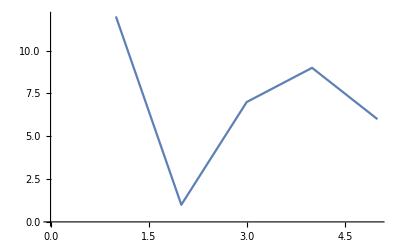

```mathematica
ListLinePlot[StringLength[TextWords["Давным-давно, в далекой галактике, далеко"]]]
(*LisrLinePLot строит прямую через точки , textwords разбивает строку на слова*)
```

8. Найдите максимальную длину слова среди английских слов из WordList []

```mathematica
max = Max[StringLength[WordList["CommonWords",Language->"English"]]](*wordlist выводит список английских слов, max выводит максимальное значение*)
```

23

```mathematica
list = Sort[WordList["CommonWords",Language->"English"],StringLength[#] > 22 &]
```

{electroencephalographic,zygotic,zygote,zydeco,zwieback,zucchini,zounds,zoophyte,zoom,zoology,zoologist,zoological,zoo,zoning,zone,zonal,zombie,zodiacal,zodiac,zloty,zither,zit,zirconium,39130,abbreviate,abbot,abbey,abbess,abbe,abattoir,abatement,abate,abashment,abashed,abash,abasement,abase,abandonment,abandoned,abandon,abalone,abaft,abacus,aback,aardvark,aah,a}
 |  |  |  |

```mathematica
First[list]
```

electroencephalographic

```mathematica
WordList["CommonWords",Language->"English"]
```

{a,aah,aardvark,aback,abacus,abaft,abalone,abandon,abandoned,abandonment,abase,abasement,abash,abashed,abashment,abate,abatement,abattoir,abbe,abbess,abbey,abbot,abbreviate,abbreviated,39128,zippy,zircon,zirconium,zit,zither,zloty,zodiac,zodiacal,zombie,zonal,zone,zoning,zoo,zoological,zoologist,zoology,zoom,zoophyte,zounds,zucchini,zwieback,zydeco,zygote,zygotic}
 |  |  |  |

```mathematica
String
```

9. Используйте Length, чтобы найти длину русского алфавита.

```mathematica
Length[Alphabet["Russian"]](*length выводит число символов*)
```

33

10. Создайте строку из заглавных букв греческого алфавита в обратном порядке.

```mathematica
StringJoin[Reverse[ToUpperCase[Alphabet["Greek"]]]]
```

ΩΨΧΦΥΤΣΡΠΟΞΝΜΛΚΙΘΗΖΕΔΓΒΑ

Раздел 1.3

1. Используйте Range и чистую функцию для создания списка из квадратов первых 20 
натуральных чисел.

```mathematica
#^2&[Range[20]](*# обозначает первый аргумент чистой функции*)
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

2. Составьте список из результатов смешивания желтого, зеленого и синего цветов с красным
цветом.

```mathematica
List[Blend[{#,Red},1/2]]&/@{Yellow,Green,Blue}
(*blend смешивает цвета , где первые два аргумента это цвета, а третий это в каком отношении смешивается*)
```

{{RGBColor[1, Rational[1, 2], 0]},{RGBColor[Rational[1, 2], Rational[1, 2], 0]},{RGBColor[Rational[1, 2], 0, Rational[1, 2]]}}

3. Создайте список столбцов в рамках, содержащих прописные и строчные версии каждой
буквы алфавита.

```mathematica
Framed[Column[{#,ToUpperCase[#]}]]&/@Alphabet[]
```

{a
A,b
B,c
C,d
D,e
E,f
F,g
G,h
H,i
I,j
J,k
K,l
L,m
M,n
N,o
O,p
P,q
Q,r
R,s
S,t
T,u
U,v
V,w
W,x
X,y
Y,z
Z}

4. Составьте список букв алфавита в случайных цветах в рамках, имеющих случайные цвета
фона.

```mathematica
Style[Framed[#,Background->RandomColor[],FrameStyle->RandomColor[]]]&/@Alphabet[]
(*style форматирует выражения с ипольз. опред параметров*)
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

5. Напишите в более простой форме команду (#^2+1&)/@Range[10]

```mathematica
Range[10]^2+1
```

{2,5,10,17,26,37,50,65,82,101}

Раздел 1.4

1. Составьте список результатов использования функции Blur до 10 раз, начиная с
растрированного размера 30 “X” (Используйте: Rasterize[Style).

```mathematica
NestList[Blur,Rasterize[Style[x],RasterSize->30],10]
(*nestlist создает список результатов применения функции*)
(*rasterise возвращает растеризованную версию выражения*)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

2. Начните с x, затем создайте список, использовав последовательно функцию Framed до 10
раз, используя каждый раз случайный цвет фона.

```mathematica
NestList[Style[Framed[#], Background->RandomColor[]]&,x,10]
```

{x,x,x,x,x,x,x,x,x,x,x}

3. Начните с размера 50 для “A”, затем создайте список вложенного применения Framed и случайного вращения 5 раз.

```mathematica
NestList[Rotate[Framed[Rasterize[#,RasterSize -> 50]],Pi*Random[]*2]&,A,5]
(*rotate поворачивает против часовой стрелки объект на опред. кол-во радиан*)
```

{A,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

4. Создайте линейный график из 100 итераций логического итерационного отображения 4 #(1-
#)&, начиная с 0.2.

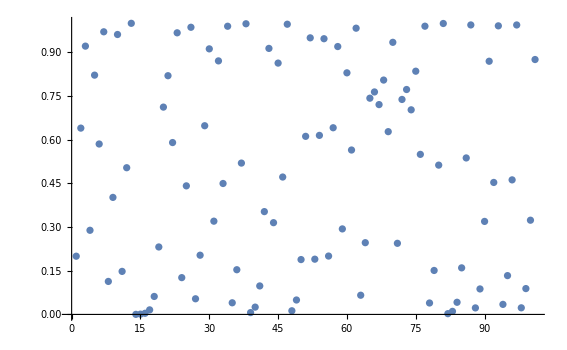

```mathematica
ListPlot[NestList[4*#*(1-#)&,0.2,100]]
```

5. Найдите числовое значение результата из 30 итераций применения функции 1+1/#&,
начиная с 1

```mathematica
Nest[1+1/#&,1,30]
```

2178309/1346269

6. Создайте список из первых 10 степеней 3 (начиная с 0) путем вложенного умножения.

```mathematica
Table[3^(#-1)&,{i,10}]
```

{1,3,9,27,81,243,729,2187,6561,19683}

7. Составьте список результатов действия вложенной функции (метод Ньютона) (# + 2 / #) / 2 до 5 раз, начиная с 1.0, а затем вычтите 2 из всех результатов.

```mathematica
list1 = NestList[((#+2/#)/2)&,1.0,5];
List[# - Sqrt[2]&/@list1]
```

{{-0.414214,0.0857864,0.0024531,2.1239×10^-6,1.59472×10^-12,-2.22045×10^-16}}

8. Создайте список из 5 степеней числа 2, т. е. 2 ^ 2 ^ 2 ... ^ 2 n раз, причем n меняется от 0 до 4.

```mathematica
NestList[#^2&,2,5]
```

{2,4,16,256,65536,4294967296}

Раздел 1.5

1. Определите функцию f, которая вычисляет квадрат ее аргумента.

```mathematica
f[x_]:=x^2
f[3]
```

9

2. Определите функцию poly, которая имеет целочисленное значение аргумента и создает
изображение оранжевого правильного многоугольника с числом сторон, равным значению
этого аргумента.

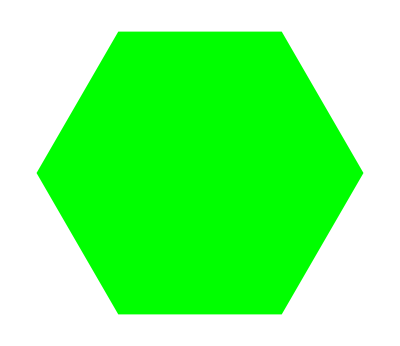

```mathematica
poly[x_]:=Graphics[{Green,Polygon[CirclePoints[x]]}]
poly[6]
(*CirclePoints дает положения n точек, равномерно распределенных по единичному кругу.*)
```

3. Определите функцию f, которая берет список из двух элементов и помещает их в обратном
порядке.

```mathematica
f[x_,y_] := Reverse[{x,y}]
f[1,2]
```

{2,1}

4. Определите функцию f, которая имеет два аргумента и дает результат в виде дроби, где
числитель равен произведению этих элементов, а знаменатель - их сумме.

```mathematica
f[x_,y_]:=(x*y)/(x+y)
f[4,5]
```

20/9

5. Определите функцию f, которая имеет два аргумента и дает результат в виде списка трех
элементов, которые соответственно равны сумме, разности и частному этих аргументов.

```mathematica
f[x_,y_]:={x+y,x-y,x/y}
f[3,4]
```

{7,-1,3/4}

6. Определите функцию evenodd, которая зависит от одного целочисленного аргумента и
имеет значение Black, если ее аргумент четный, значение - White в противном случае, значение
Red - если аргумент равен нулю.

```mathematica
evenodd[x_]:= If[x≠0,If[EvenQ[x],Black,White],Red]
evenodd[4]
evenodd[0]
evenodd[3]
(*if (условие верности , если выполняется условие, если не выполняется, всли нм то и ни то )*)
(*EvenQ дает true если число является четным целым*)
```

GrayLevel[0]

RGBColor[1, 0, 0]

GrayLevel[1]

7. Определите функцию Fibonacci f с f [0]=1 и f [1]=1, а f [n] для натурального числа n является
суммой f [n-1] и f [n-2].

```mathematica
fibonacci[0]:=1
fibonacci[1]:=1
fibonacci[n_]:= fibonacci[n-1]+fibonacci[n-2]
fibonacci[6]
```

8

```mathematica
Fibonacci[6]
```

8